```mathematica
ClearAll["Global`*"]
```

```mathematica
ps=Range[0.01,50,0.1];
```

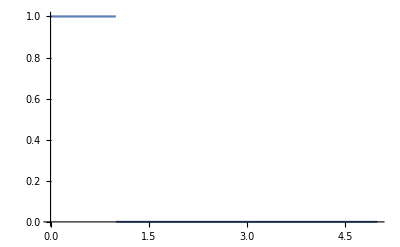

```mathematica
ϕ[r_]=HeavisideTheta[1-r];
Plot[ϕ[r],{r,0,5}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {1.00494}. NIntegrate obtained -0.317965 and 0.000806564 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {1.00494}. NIntegrate obtained -0.322817 and 0.000817644 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {1.00494}. NIntegrate obtained -0.331199 and 0.000835509 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

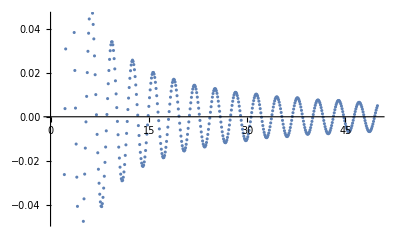

```mathematica
ϕ[r_]=HeavisideTheta[1-r];
ps=Range[0.01,50,0.1];

dr=0.01;
rmin=0.01;
rmax=10;
rs=Range[rmin,rmax,dr];

fNintps=NIntegrate[r*ps*ϕ[r]*BesselJ[0,r*ps]*BesselY[1,ps],{r,rmin,rmax}];
fSum[p_]=dr*Total[rs*p*ϕ[rs]*BesselJ[0,rs*p]*BesselY[1,p]];
fSumps=fSum[ps];

A=ListPlot[{
Transpose@{ps,fNintps},
Transpose@{ps,fSumps}
}]
```

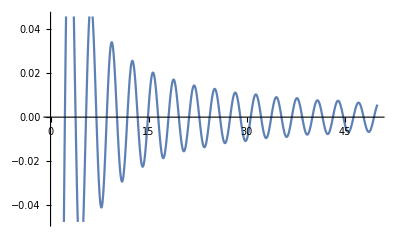

```mathematica
f[p_]=Integrate[r*p*ϕ[r]*BesselJ[0,r*p]*BesselY[1,p],{r,rmin,rmax}];
B=Plot[f[p],{p,0,50}]
```

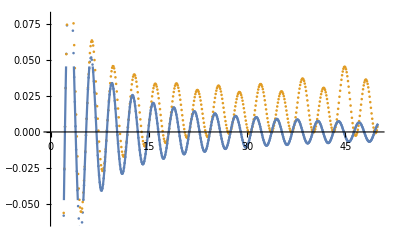

```mathematica
Show[A,B]
```

```mathematica
Install["/media/tobias/data/OneDrive/projects/MasterThesis_HeavyIonCollisions/code/Mathematica/Cuhre-Linux"]
Install["/media/tobias/data/OneDrive/projects/MasterThesis_HeavyIonCollisions/code/Mathematica/Vegas-Linux"]
Install["/media/tobias/data/OneDrive/projects/MasterThesis_HeavyIonCollisions/code/Mathematica/Suave-Linux"]
Install["/media/tobias/data/OneDrive/projects/MasterThesis_HeavyIonCollisions/code/Mathematica/Divonne-Linux"]
```

LinkObject[…]

LinkObject[…]

LinkObject[…]

«1 more identical outputs»

```mathematica
f[x_,y_]=(1+x*y)/(√(2+x^2));
Cuhre[1/(√(1-y^2)√(f[x,y]^2-1)),{x,0.5,10},{y,(√(2+x^2)-1)/x,1},Verbose->0]
```

Cuhre::success: Needed 9035 function evaluations on 70 subregions.

{{15.96,0.0151969,4.4213×10^-18}}

```mathematica
Suave[1/(√(1-y^2)√(f[x,y]^2-1)),{x,0.5,10},{y,(√(2+x^2)-1)/x,1},Verbose->0]
```

Suave::accuracy: Desired accuracy was not reached within 50000 function evaluations on 50 subregions.

{{15.9259,0.0161759,1.}}

```mathematica
Vegas[1/(√(1-y^2)√(f[x,y]^2-1)),{x,0.5,10},{y,(√(2+x^2)-1)/x,1},Verbose->0]
```

Vegas::success: Needed 32500 function evaluations.

{{15.9493,0.0153094,0.0119089}}

```mathematica
ClearAll["Global`*"]
ma=0.6;
mb=0.14;
mc=0.14;
pabc=Sqrt[((ma+mb)^2-mc^2)*((ma-mb)^2-mc^2)]/(2*ma);
Eabc=Sqrt[mb^2+pabc^2];
w[p_,m_]=Sqrt[p*p+m*m];
Q=1;
absgradg[t_,u_,v_,p_]=√((-t*u*w[p,mb]/w[t*Q,ma]*Q^2+Q*p*v)^2+(w[t*Q,ma]*w[p,mb])^2+(t*Q*p)^2);
areafactor[t_,v_,p_]=√((v*(p*Q)/(w[p,mb]*w[t*Q,ma])*(1-(t^2*Q^2)/w[t*Q,ma]^2))^2+(1)^2+((t*Q*p)/(w[t*Q,ma]*w[p,mb]))^2);
ustar[t_,v_,p_]=(ma*Eabc+Q*p*t*v)/(w[t*Q,ma]*w[p,mb]);
Integrand[t_,v_,p_]=If[ustar[t,v,p]>1,t*1/(√(ustar[t,v,p]^2-1))*1/(√(1-v^2))*areafactor[t,v,p]/absgradg[t,ustar[t,v,p],v,p],0];
```

```mathematica
Plot3D[Integrand[t,v,0.5],{t,0,5},{v,0.8,1}]
```

-Graphics3D-

```mathematica
Install[StringJoin[NotebookDirectory[],"Cuhre-Linux"]];
Install[StringJoin[NotebookDirectory[],"Vegas-Linux"]];
```

LinkOpen::linke: Specified file is not a MathLink executable..

```mathematica
Cuhre[Integrand[t,v,p],{t,0,1},{v,-1,1},Verbose->0,MaxPoints->100000]
```

Cuhre[If[(0.990342 (0.18+t v))/(√(0.36+t^2))>1,areafactor[t,v,1]/(√(ustar[t,v,1]^2-1) √(1-v^2) absgradg[t,ustar[t,v,1],v,1]),0],{t,0,1},{v,-1,1},Verbose→0,MaxPoints→100000]

```mathematica
s=Solve[1==(A+B*t*v)/(w[t*C,D]*w[F,G]),v]
```

{{v→-(√(F^2+G^2) √(D^2+C^2 t^2) (-1+A/(√(F^2+G^2) √(D^2+C^2 t^2))))/(B t)}}

```mathematica
vmin[t_]=v/.s[[1]]
```

-(√(F^2+G^2) √(D^2+C^2 t^2) (-1+A/(√(F^2+G^2) √(D^2+C^2 t^2))))/(B t)

```mathematica
tmin=t/.Solve[0==D[vmin[t],t],t][[2]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

(√(-A^2 D^2+D^4 F^2+D^4 G^2))/(A C)

```mathematica
vmin[tmin]//FullSimplify
```

(A C (-A+√(F^2+G^2) √((D^4 (F^2+G^2))/A^2)))/(B √(-A^2 D^2+D^4 (F^2+G^2)))

```mathematica
Manipulate[
Plot3D[Integrand[t,v,p],{t,0,5},{v,-1,1},PlotRange->{All,All,{-1,1}}],
{p,0,2}]
```

```mathematica
ustar[1,1,1]
```

1.00207